```mathematica
Flatten[Table[{Subscript[l, c,b],0,2},{b,1,3},{c,1,b-1}],1]
```

{{l_(1,2),0,2},{l_(1,3),0,2},{l_(2,3),0,2}}

```mathematica
ν1⟦1,1⟧
```

0

```mathematica
ClearAll[b]
```

```mathematica
ClearAll[t]
```

```mathematica
ClearAll[b]
```

```mathematica
HoldAll
```

```mathematica
CombSum[r_,i_,n_,α_,ν_,s_]:=Block[{t},(((2i)!)^n r^(n*i)Gamma[n/2(α+1)])/Gamma[n/2+n*i]*Sum[1/((2r)^(∑_(a=1)^n Subscript[q, a])∏_(a=1)^n (Subscript[q, a]!))*Sum[∏_(b=1)^n ∏_(c=1)^(b-1) (t⟦c,b⟧*Subscript[s, c,b])^Subscript[l, c,b]/(Subscript[l, c,b]!)∏_(s=1)^n Boole[∑_(e=1)^(s-1) Subscript[l, e,s]+∑_(e=s+1)^n Subscript[l, s,e]==2i-2 Subscript[q, s]],Evaluate[Sequence@@Flatten[Table[{Subscript[l, c,b],0,2i},{b,1,n},{c,1,b-1}],1]]],Evaluate[Sequence@@Table[{Subscript[q, a],0,i},{a,1,n}]]]/.t->ν]
CombSum[r_,i_,1,α_,ν_,s_]:=((2i)!Gamma[1/2(α+1)])/Gamma[1/2+i]*1/(2^i i!)
```

```mathematica
CombSum[0,4,4,4/3,ν,s]
```

$Aborted

```mathematica
CombSum[0.9,2,3,4/3,ν,s]
```

13.0476 (0.00367515+0.023815 ν⟦1,2⟧^2 s_(1,2)^2+0.00643004 ν⟦1,2⟧^4 s_(1,2)^4+0.023815 ν⟦1,3⟧^2 s_(1,3)^2+0.0771605 ν⟦1,2⟧^2 ν⟦1,3⟧^2 s_(1,2)^2 s_(1,3)^2+0.00643004 ν⟦1,3⟧^4 s_(1,3)^4+0.171468 ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2) s_(1,3) s_(2,3)+0.0925926 ν⟦1,2⟧^3 ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2)^3 s_(1,3) s_(2,3)+0.0925926 ν⟦1,2⟧ ν⟦1,3⟧^3 ν⟦2,3⟧ s_(1,2) s_(1,3)^3 s_(2,3)+0.023815 ν⟦2,3⟧^2 s_(2,3)^2+0.0771605 ν⟦1,2⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(2,3)^2+0.0771605 ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,3)^2 s_(2,3)^2+0.125 ν⟦1,2⟧^2 ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(1,3)^2 s_(2,3)^2+0.0925926 ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧^3 s_(1,2) s_(1,3) s_(2,3)^3+0.00643004 ν⟦2,3⟧^4 s_(2,3)^4)

```mathematica
Factor[Total[OOperator[3,CombSum[γ,2,#1,α,#2,#3]&]]]
```

(4096 γ^3 (2+3 γ+4 γ^2+2 γ^3) Gamma[(3 (1+α))/2])/(5005 √π)

```mathematica
CombSum[γ,2,3,α,ν,s]
```

1/(5005 √π)65536 γ^6 Gamma[(3 (1+α))/2] (1/(512 γ^6)+(ν⟦1,2⟧^2 s_(1,2)^2)/(64 γ^4)+(ν⟦1,2⟧^4 s_(1,2)^4)/(192 γ^2)+(ν⟦1,3⟧^2 s_(1,3)^2)/(64 γ^4)+(ν⟦1,2⟧^2 ν⟦1,3⟧^2 s_(1,2)^2 s_(1,3)^2)/(16 γ^2)+(ν⟦1,3⟧^4 s_(1,3)^4)/(192 γ^2)+(ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2) s_(1,3) s_(2,3))/(8 γ^3)+(ν⟦1,2⟧^3 ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2)^3 s_(1,3) s_(2,3))/(12 γ)+(ν⟦1,2⟧ ν⟦1,3⟧^3 ν⟦2,3⟧ s_(1,2) s_(1,3)^3 s_(2,3))/(12 γ)+(ν⟦2,3⟧^2 s_(2,3)^2)/(64 γ^4)+(ν⟦1,2⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(2,3)^2)/(16 γ^2)+(ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,3)^2 s_(2,3)^2)/(16 γ^2)+1/8 ν⟦1,2⟧^2 ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(1,3)^2 s_(2,3)^2+(ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧^3 s_(1,2) s_(1,3) s_(2,3)^3)/(12 γ)+(ν⟦2,3⟧^4 s_(2,3)^4)/(192 γ^2))

```mathematica
Factor[CombSum[γ,2,3,α,ν,s]/.{Subscript[s, 1,2]->1,Subscript[s, 1,3]->1,Subscript[s, 2,3]->1}/.ν->({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})]
```

(128 (1+24 γ^2+64 γ^3+104 γ^4+128 γ^5+64 γ^6) Gamma[(3 (1+α))/2])/(5005 √π)

```mathematica
128*64
```

8192

```mathematica
128*104
```

13312

```mathematica
4096*3
```

12288

```mathematica
CombSum[γ,2,3,α,ν,s]
```

1/(5005 √π)65536 γ^6 Gamma[(3 (1+α))/2] (1/(512 γ^6)+(s_(1,2)^2)/(64 γ^4)+(s_(1,2)^4)/(192 γ^2)+((ν⟦1⟧⟦3⟧)^2 s_(1,3)^2)/(64 γ^4)+((ν⟦1⟧⟦3⟧)^2 s_(1,2)^2 s_(1,3)^2)/(16 γ^2)+((ν⟦1⟧⟦3⟧)^4 s_(1,3)^4)/(192 γ^2)+(ν⟦1⟧⟦3⟧ ν⟦2⟧⟦3⟧ s_(1,2) s_(1,3) s_(2,3))/(8 γ^3)+(ν⟦1⟧⟦3⟧ ν⟦2⟧⟦3⟧ s_(1,2)^3 s_(1,3) s_(2,3))/(12 γ)+((ν⟦1⟧⟦3⟧)^3 ν⟦2⟧⟦3⟧ s_(1,2) s_(1,3)^3 s_(2,3))/(12 γ)+((ν⟦2⟧⟦3⟧)^2 s_(2,3)^2)/(64 γ^4)+((ν⟦2⟧⟦3⟧)^2 s_(1,2)^2 s_(2,3)^2)/(16 γ^2)+((ν⟦1⟧⟦3⟧)^2 (ν⟦2⟧⟦3⟧)^2 s_(1,3)^2 s_(2,3)^2)/(16 γ^2)+1/8 (ν⟦1⟧⟦3⟧)^2 (ν⟦2⟧⟦3⟧)^2 s_(1,2)^2 s_(1,3)^2 s_(2,3)^2+(ν⟦1⟧⟦3⟧ (ν⟦2⟧⟦3⟧)^3 s_(1,2) s_(1,3) s_(2,3)^3)/(12 γ)+((ν⟦2⟧⟦3⟧)^4 s_(2,3)^4)/(192 γ^2))

```mathematica
CombSum[γ,3,2,α,ν,s]
```

720 γ^6 Gamma[1+α] (1/(2304 γ^6)+(ν⟦1,2⟧^2 s_(1,2)^2)/(128 γ^4)+(ν⟦1,2⟧^4 s_(1,2)^4)/(96 γ^2)+1/720 ν⟦1,2⟧^6 s_(1,2)^6)

```mathematica
(*все неприсутствующие Subscript[s, ab] исчезают автоматом, так что по ним можно ничего не делать*)
```

```mathematica
CombSum[γ,4,3,α,ν1,s]
```

1/(5311735 √π)360777252864 γ^12 Gamma[(3 (1+α))/2] (1/(56623104 γ^12)+(s_(1,2)^2)/(1769472 γ^10)+(s_(1,2)^4)/(589824 γ^8)+(s_(1,2)^6)/(1105920 γ^6)+(s_(1,2)^8)/(15482880 γ^4)+(s_(1,3)^2)/(1769472 γ^10)+(s_(1,2)^2 s_(1,3)^2)/(73728 γ^8)+(s_(1,2)^4 s_(1,3)^2)/(36864 γ^6)+(s_(1,2)^6 s_(1,3)^2)/(138240 γ^4)+(s_(1,3)^4)/(589824 γ^8)+(s_(1,2)^2 s_(1,3)^4)/(36864 γ^6)+(s_(1,2)^4 s_(1,3)^4)/(36864 γ^4)+(s_(1,3)^6)/(1105920 γ^6)+(s_(1,2)^2 s_(1,3)^6)/(138240 γ^4)+(s_(1,3)^8)/(15482880 γ^4))

```mathematica
CombSum[γ,1,4,α]
```

0

```mathematica
CombSum[γ,1,4,α,ν,s]
```

2/15 γ^4 Gamma[2 (1+α)] (1/(16 γ^4)+(ν⟦1,2⟧^2 s_(1,2)^2)/(8 γ^2)+(ν⟦1,3⟧^2 s_(1,3)^2)/(8 γ^2)+(ν⟦1,4⟧^2 s_(1,4)^2)/(8 γ^2)+(ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2) s_(1,3) s_(2,3))/(2 γ)+(ν⟦2,3⟧^2 s_(2,3)^2)/(8 γ^2)+1/4 ν⟦1,4⟧^2 ν⟦2,3⟧^2 s_(1,4)^2 s_(2,3)^2+(ν⟦1,2⟧ ν⟦1,4⟧ ν⟦2,4⟧ s_(1,2) s_(1,4) s_(2,4))/(2 γ)+ν⟦1,3⟧ ν⟦1,4⟧ ν⟦2,3⟧ ν⟦2,4⟧ s_(1,3) s_(1,4) s_(2,3) s_(2,4)+(ν⟦2,4⟧^2 s_(2,4)^2)/(8 γ^2)+1/4 ν⟦1,3⟧^2 ν⟦2,4⟧^2 s_(1,3)^2 s_(2,4)^2+(ν⟦1,3⟧ ν⟦1,4⟧ ν⟦3,4⟧ s_(1,3) s_(1,4) s_(3,4))/(2 γ)+ν⟦1,2⟧ ν⟦1,4⟧ ν⟦2,3⟧ ν⟦3,4⟧ s_(1,2) s_(1,4) s_(2,3) s_(3,4)+ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,4⟧ ν⟦3,4⟧ s_(1,2) s_(1,3) s_(2,4) s_(3,4)+(ν⟦2,3⟧ ν⟦2,4⟧ ν⟦3,4⟧ s_(2,3) s_(2,4) s_(3,4))/(2 γ)+(ν⟦3,4⟧^2 s_(3,4)^2)/(8 γ^2)+1/4 ν⟦1,2⟧^2 ν⟦3,4⟧^2 s_(1,2)^2 s_(3,4)^2)

```mathematica
CombSum[γ,1,3,α,ν1,s]
```

(128 γ^3 Gamma[(3 (1+α))/2] (1/(8 γ^3)+(s_(1,2)^2)/(4 γ)+(s_(1,3)^2)/(4 γ)))/(105 √π)

```mathematica
ν1=({{0, 1, 1}, {1, 0, 0}, {1, 0, 0}});
```

```mathematica
DifferenceOperator[n_,ν_,s_,f_]:=Integrate[D[f,Evaluate[Sequence@@Flatten[Table[{Subscript[s, c,b],ν⟦c⟧⟦b⟧},{b,1,n},{c,1,b-1}],1]]],Evaluate[Sequence@@Flatten[Table[{Subscript[s, c,b],0,1},{b,1,n},{c,1,b-1}],1]]]
DifferenceOperator[1,ν_,s_,f_]:=f
```

```mathematica
ClearAll[ν]
```

```mathematica
DifferenceOperator[3,ν1,s,CombSum[γ,3,3,α,ν1,s]]
```

(122880 γ^4 (3+4 γ^2) Gamma[(3 (1+α))/2])/(323323 √π)

```mathematica
CombSum[γ,3,1,α,ν1,s]
```

(8 Gamma[(1+α)/2])/(√π)

```mathematica
DifferenceOperator[1,ν1,s,CombSum[γ,3,1,α,ν1,s]]
```

(8 Gamma[(1+α)/2])/(√π)

```mathematica
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicates[allConnected[n],IsomorphicGraphQ];
```

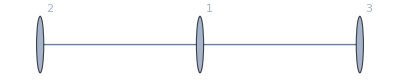
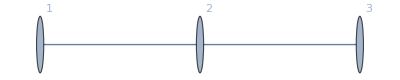
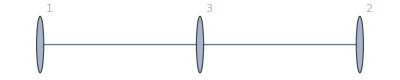
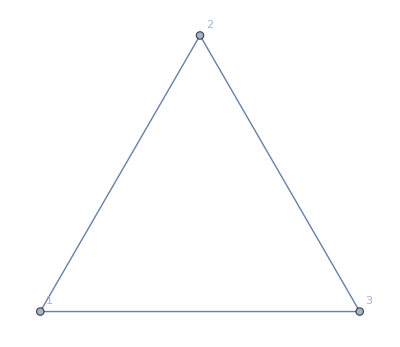

```mathematica
allConnected[3]
```

```mathematica
MatrixForm/@AdjacencyMatrix/@allConnected[3]
```

{(0 | 1 | 1
1 | 0 | 0
1 | 0 | 0),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 1
1 | 1 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}

```mathematica
Sort[%414]
```

{(0 | 0 | 1
0 | 0 | 1
1 | 1 | 0),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(0 | 1 | 1
1 | 0 | 0
1 | 0 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}

```mathematica
({#^2,#}&)/@AdjacencyMatrix/@allConnected[3]
```

{{SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…]}}

```mathematica
(*все работает, отлично!*)
```

```mathematica
OOperator[n_,f_]:=Block[{s},(DifferenceOperator[n,#,s,f[n,#,s]]&)/@AdjacencyMatrix/@allConnected[n]]
```

```mathematica
CombSum[γ,1,2,α,t,s]
```

2 γ^2 Gamma[1+α] (1/(4 γ^2)+1/2 t⟦1,2⟧^2 s_(1,2)^2)

```mathematica
(*граф на 2 вершинах, все ок*)
```

```mathematica
OOperator[2,CombSum[γ,1,#1,α,#2,#3]&]
```

{γ^2 Gamma[1+α]}

```mathematica
(*граф на 3 вершинах 2 степени, выживает только цепь, которая и есть полный граф в данном случае, все ок*)
```

```mathematica
OOperator[3,CombSum[γ,1,#1,α,#2,#3]&]
```

{0,0,0,(128 γ^3 Gamma[(3 (1+α))/2])/(105 √π)}

```mathematica
(*Чисто проверяем, что для n=1 тоже ничего не ломается*)
```

```mathematica
OOperator[1,CombSum[γ,1,#1,α,#2,#3]&]
```

{(2 Gamma[(1+α)/2])/(√π)}

```mathematica
OOperator[4,CombSum[γ,1,#1,α,#2,#3]&]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2/15 γ^4 Gamma[2 (1+α)],0,2/15 γ^4 Gamma[2 (1+α)],0,0,2/15 γ^4 Gamma[2 (1+α)],0,0,0,0,0,0,0,0,0,0,0}

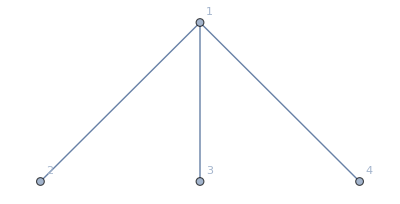
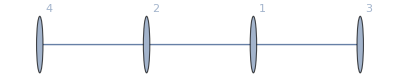
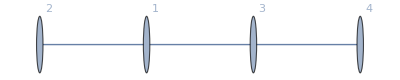
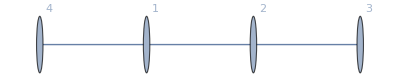
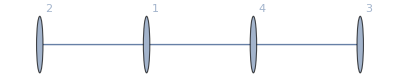
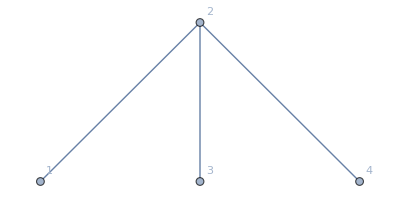
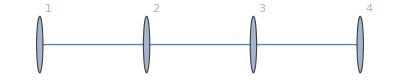
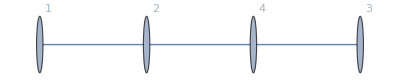

```mathematica
allConnected[4]
```

```mathematica
(*Для 2 степени и 4 вершин тоже все сходится, выживает только мах замкнутая цепь! и комб количества сходятся с уже посчитанными: их 3 шт на 4 вершинах*)
```

```mathematica
CombSum[γ,2,3,α,ν,s]
```

1/(5005 √π)65536 γ^6 Gamma[(3 (1+α))/2] (1/(512 γ^6)+(ν⟦1,2⟧^2 s_(1,2)^2)/(64 γ^4)+(ν⟦1,2⟧^4 s_(1,2)^4)/(192 γ^2)+(ν⟦1,3⟧^2 s_(1,3)^2)/(64 γ^4)+(ν⟦1,2⟧^2 ν⟦1,3⟧^2 s_(1,2)^2 s_(1,3)^2)/(16 γ^2)+(ν⟦1,3⟧^4 s_(1,3)^4)/(192 γ^2)+(ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2) s_(1,3) s_(2,3))/(8 γ^3)+(ν⟦1,2⟧^3 ν⟦1,3⟧ ν⟦2,3⟧ s_(1,2)^3 s_(1,3) s_(2,3))/(12 γ)+(ν⟦1,2⟧ ν⟦1,3⟧^3 ν⟦2,3⟧ s_(1,2) s_(1,3)^3 s_(2,3))/(12 γ)+(ν⟦2,3⟧^2 s_(2,3)^2)/(64 γ^4)+(ν⟦1,2⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(2,3)^2)/(16 γ^2)+(ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,3)^2 s_(2,3)^2)/(16 γ^2)+1/8 ν⟦1,2⟧^2 ν⟦1,3⟧^2 ν⟦2,3⟧^2 s_(1,2)^2 s_(1,3)^2 s_(2,3)^2+(ν⟦1,2⟧ ν⟦1,3⟧ ν⟦2,3⟧^3 s_(1,2) s_(1,3) s_(2,3)^3)/(12 γ)+(ν⟦2,3⟧^4 s_(2,3)^4)/(192 γ^2))

```mathematica
Factor[1/(5005 √π)65536 γ^6 Gamma[(3 (1+α))/2] ((ν⟦1,2⟧^2 ν⟦1,3⟧^2 Subscript[s, 1,2]^2 Subscript[s, 1,3]^2)/(16 γ^2))]
```

(4096 γ^4 Gamma[(3 (1+α))/2] ν⟦1,2⟧^2 ν⟦1,3⟧^2 s_(1,2)^2 s_(1,3)^2)/(5005 √π)

```mathematica
(*Для 4 степени и 3 вершин тоже все сходится! видимо, все действительно ок*)
```

```mathematica
OOperator[3,CombSum[γ,2,#1,α,#2,#3]&]
```

{(4096 γ^4 Gamma[(3 (1+α))/2])/(5005 √π),(4096 γ^4 Gamma[(3 (1+α))/2])/(5005 √π),(4096 γ^4 Gamma[(3 (1+α))/2])/(5005 √π),(8192 γ^3 (1+2 γ^2+γ^3) Gamma[(3 (1+α))/2])/(5005 √π)}

```mathematica
wHSn[M_,r_,z_,n_,α_]:=((-1)^(n-1)z^n)/(n!)2^(n*α/2)∑_(q=0)^M ∑_(i=0)^q (2q+1/2)2^(4q-n*i+1)Binomial[2q,2i]Binomial[q+i-1/2,2q](∑_(p=0)^q Binomial[2q,2p]Binomial[q+p-1/2,2q]*1/(2p+α+1))*OOperator[n,CombSum[r,i,#1,α,#2,#3]&]
```

```mathematica
(*r =γ, z=vG(0)^(α/2)*)
```

```mathematica
wHSn[2,0.9,z,3,4/3]
```

0.14253 z^3

```mathematica
(*было только от полного графа, как раз третье слагаемое в OOperator, 0.15972538101574535 z^3*)
```

```mathematica
wHSn[2,0.9,z,2,4/3]
```

-0.284602 z^2

```mathematica
wHSn[2,0.9,z,2,4/3]
```

```mathematica
wHSn[2,0.9,z,1,4/3]
```

(1665 2^(2/3) z Gamma[7/6])/(1729 √π)

```mathematica
HS[2,2,γ,z,α]
```

HS[2,2,γ,z,α]

```mathematica
HS[n0_,M_,r_,z_,α_]:=∑_(n=1)^n0 wHSn[M,r,z,n,α]
```

```mathematica
Expand[FullSimplify[HS[2,2,γ,z,α]]]
```

(15 2^(α/2) z Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α))+(15 2^(α/2) z α Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α))+(15 2^(α/2) z α^2 Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α))-(735 2^(-7+α) z^2 α γ^2 Gamma[1+α])/((1+α) (3+α) (5+α))-(105 2^(-8+α) z^2 α^2 γ^2 Gamma[1+α])/((1+α) (3+α) (5+α))+(315 2^(-7+α) z^2 α γ^4 Gamma[1+α])/((1+α) (3+α) (5+α))-(315 2^(-8+α) z^2 α^2 γ^4 Gamma[1+α])/((1+α) (3+α) (5+α))

```mathematica
Expand[N[hs33gen]]
```

(0.00361572 2.^(14.+0.5 α) z Gamma[0.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.00771353 2.^(14.+0.5 α) z α Gamma[0.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.00144629 2.^(14.+0.5 α) z α^2 Gamma[0.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.000964191 2.^(14.+0.5 α) z α^3 Gamma[0.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.461426 2.^α z^2 α γ^2 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))-(39.1058 2.^α z^2 α^2 γ^2 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))+(4.67194 2.^α z^2 α^3 γ^2 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))-(6.76758 2.^α z^2 α γ^4 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))+(11.8433 2.^α z^2 α^2 γ^4 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))-(4.22974 2.^α z^2 α^3 γ^4 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))-(11.7305 2.^α z^2 α γ^6 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))+(8.79785 2.^α z^2 α^2 γ^6 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))-(1.46631 2.^α z^2 α^3 γ^6 Gamma[1.+α])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.00175485 2.^(13.+1.5 α) z^3 α γ^3 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.000553263 2.^(13.+1.5 α) z^3 α^2 γ^3 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.0000445307 2.^(13.+1.5 α) z^3 α^3 γ^3 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.00102917 2.^(13.+1.5 α) z^3 α γ^4 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.000676522 2.^(13.+1.5 α) z^3 α^2 γ^4 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.0000809671 2.^(13.+1.5 α) z^3 α^3 γ^4 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.00121871 2.^(13.+1.5 α) z^3 α γ^5 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.000786889 2.^(13.+1.5 α) z^3 α^2 γ^5 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.0000887661 2.^(13.+1.5 α) z^3 α^3 γ^5 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.000302316 2.^(13.+1.5 α) z^3 α γ^6 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.000163164 2.^(13.+1.5 α) z^3 α^2 γ^6 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(6.00303×10^-6 2.^(13.+1.5 α) z^3 α^3 γ^6 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.000470795 2.^(13.+1.5 α) z^3 α γ^7 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.000353096 2.^(13.+1.5 α) z^3 α^2 γ^7 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.0000588494 2.^(13.+1.5 α) z^3 α^3 γ^7 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.00030704 2.^(13.+1.5 α) z^3 α γ^8 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.00023028 2.^(13.+1.5 α) z^3 α^2 γ^8 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.00003838 2.^(13.+1.5 α) z^3 α^3 γ^8 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.0000909748 2.^(13.+1.5 α) z^3 α γ^9 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))-(0.0000682311 2.^(13.+1.5 α) z^3 α^2 γ^9 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))+(0.0000113719 2.^(13.+1.5 α) z^3 α^3 γ^9 Gamma[1.5 (1.+α)])/((1.+α) (3.+α) (5.+α) (7.+α))

```mathematica
hs33gen=Simplify[Expand[FullSimplify[HS[3,3,γ,z,α]]]]
```

(88179 2^(14+α/2) z (15+32 α+6 α^2+4 α^3) Gamma[(1+α)/2]-264537 2^α √π z^2 α γ^2 (8 (-45+660 γ^2+1144 γ^4)-6 α (-5085+1540 γ^2+1144 γ^4)+α^2 (-3645+3300 γ^2+1144 γ^4)) Gamma[1+α]+2^(13+(3 α)/2) z^3 α γ^3 (8 (80244-47061 γ-55728 γ^2-13824 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)-6 α (33732-41247 γ-47976 γ^2-9948 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)+α^2 (16290-29619 γ-32472 γ^2-2196 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)) Gamma[(3 (1+α))/2])/(206389248 √π (1+α) (3+α) (5+α) (7+α))

```mathematica
Factor[(33732-41247 γ-47976 γ^2-9948 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)]
```

33732-41247 γ-47976 γ^2-9948 γ^3+21528 γ^4+14040 γ^5+4160 γ^6

```mathematica
Factor[(15+32 α+6 α^2+4 α^3)]
```

(1+2 α) (15+2 α+2 α^2)

```mathematica
FactorInteger[264537/9]
```

{{7,1},{13,1},{17,1},{19,1}}

```mathematica
FactorInteger[88179]
```

{{3,1},{7,1},{13,1},{17,1},{19,1}}

```mathematica
FactorInteger[206389248 ]
```

{{2,14},{3,1},{13,1},{17,1},{19,1}}

```mathematica
206389248/2^14
```

12597

```mathematica
Factor[8 (80244-47061 γ-55728 γ^2-13824 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)]
```

8 (80244-47061 γ-55728 γ^2-13824 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)

```mathematica
FactorTerms[(88179 2^(14+α/2) z (15+32 α+6 α^2+4 α^3) Gamma[(1+α)/2]-264537 2^α √π z^2 α γ^2 (8 (-45+660 γ^2+1144 γ^4)-6 α (-5085+1540 γ^2+1144 γ^4)+α^2 (-3645+3300 γ^2+1144 γ^4)) Gamma[1+α]+2^(13+(3 α)/2) z^3 α γ^3 (8 (80244-47061 γ-55728 γ^2-13824 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)-6 α (33732-41247 γ-47976 γ^2-9948 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)+α^2 (16290-29619 γ-32472 γ^2-2196 γ^3+21528 γ^4+14040 γ^5+4160 γ^6)) Gamma[(3 (1+α))/2])/(206389248 √π (1+α) (3+α) (5+α) (7+α))]
```

1/206389248((1322685 2^(14+α/2) z Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α) (7+α))+(88179 2^(19+α/2) z α Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α) (7+α))+(264537 2^(15+α/2) z α^2 Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α) (7+α))+(88179 2^(16+α/2) z α^3 Gamma[(1+α)/2])/(√π (1+α) (3+α) (5+α) (7+α))+(11904165 2^(3+α) z^2 α γ^2 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))-(4035511935 2^(1+α) z^2 α^2 γ^2 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))+(964237365 2^α z^2 α^3 γ^2 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))-(43648605 2^(5+α) z^2 α γ^4 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))+(305540235 2^(3+α) z^2 α^2 γ^4 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))-(218243025 2^(2+α) z^2 α^3 γ^4 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))-(37828791 2^(6+α) z^2 α γ^6 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))+(113486373 2^(4+α) z^2 α^2 γ^6 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))-(37828791 2^(3+α) z^2 α^3 γ^6 Gamma[1+α])/((1+α) (3+α) (5+α) (7+α))+(20061 2^(18+(3 α)/2) z^3 α γ^3 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(25299 2^(16+(3 α)/2) z^3 α^2 γ^3 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(8145 2^(14+(3 α)/2) z^3 α^3 γ^3 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(47061 2^(16+(3 α)/2) z^3 α γ^4 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(123741 2^(14+(3 α)/2) z^3 α^2 γ^4 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(29619 2^(13+(3 α)/2) z^3 α^3 γ^4 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(3483 2^(20+(3 α)/2) z^3 α γ^5 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(17991 2^(17+(3 α)/2) z^3 α^2 γ^5 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(4059 2^(16+(3 α)/2) z^3 α^3 γ^5 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(27 2^(25+(3 α)/2) z^3 α γ^6 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(7461 2^(16+(3 α)/2) z^3 α^2 γ^6 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(549 2^(15+(3 α)/2) z^3 α^3 γ^6 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(2691 2^(19+(3 α)/2) z^3 α γ^7 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(8073 2^(17+(3 α)/2) z^3 α^2 γ^7 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(2691 2^(16+(3 α)/2) z^3 α^3 γ^7 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(1755 2^(19+(3 α)/2) z^3 α γ^8 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(5265 2^(17+(3 α)/2) z^3 α^2 γ^8 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(1755 2^(16+(3 α)/2) z^3 α^3 γ^8 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(65 2^(22+(3 α)/2) z^3 α γ^9 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))-(195 2^(20+(3 α)/2) z^3 α^2 γ^9 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α))+(65 2^(19+(3 α)/2) z^3 α^3 γ^9 Gamma[(3 (1+α))/2])/(√π (1+α) (3+α) (5+α) (7+α)))

```mathematica
hs33gen
```

```mathematica
hs44gen=Simplify[Expand[FullSimplify[HS[4,4,γ,z,α]]]]
```

$Aborted

```mathematica
hs32=HS[3,2,0.5,z,4/3]
```

-0.0950143 z^2+0.029515 z^3+(1665 2^(2/3) z Gamma[7/6])/(1729 √π)

```mathematica
hs42=N[HS[4,2,0.5,z,4/3]]
```

$Aborted

```mathematica
hs35=HS[3,5,0.5,z,4/3]
```

$Aborted

```mathematica
hs36=HS[3,6,0.5,z,4/3]
```

0.82505 z-0.0764946 z^2+0.0349095 z^3

```mathematica
hs43=HS[4,3,0.5,z,4/3]
```

0.848084 z-0.080886 z^2+0.0342595 z^3+0.0000502965 z^4

```mathematica
hs33=HS[3,3,0.5,z,4/3]
```

0.848084 z-0.080886 z^2+0.0342595 z^3

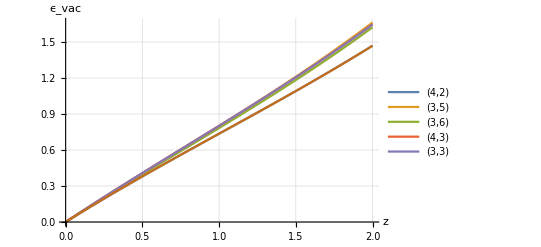

```mathematica
pl1=Plot[{hs42,hs35,hs36,hs43,hs33,hs32},{z,0,2},PlotLegends->{"(4,2)","(3,5)", "(3,6)","(4,3)","(3,3)"},GridLines->Automatic,AxesLabel-> {"z","ϵ_vac"}]
```

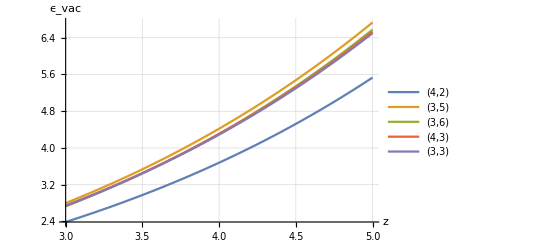

```mathematica
pl2=Plot[{hs42,hs35,hs36,hs43,hs33},{z,3,5},PlotLegends->{"(4,2)","(3,5)", "(3,6)","(4,3)","(3,3)"},GridLines->Automatic,AxesLabel-> {"z","ϵ_vac"}]
```

```mathematica
pl3=Plot3D[Evaluate[HS[3,3,γ,z,4/3]],{z,0,5},{γ,0,1},AxesLabel-> {"z","γ","ϵ_vac"},PlotPoints->100]
```

-Graphics3D-

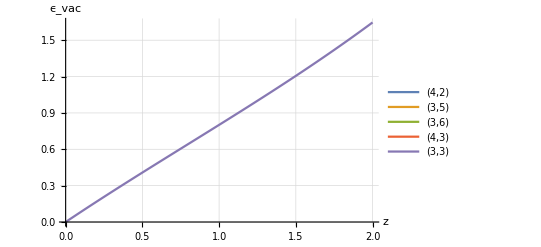

```mathematica
pl4=Plot[{hs42,hs35,hs36,hs43,hs33},{z,0,2},PlotLegends->{"(4,2)","(3,5)", "(3,6)","(4,3)","(3,3)"},GridLines->Automatic,AxesLabel-> {"z","ϵ_vac"}]
```

```mathematica
N[Expand@hs33gen/.{α->4/3,γ->0.5}]
```

0.848084 z-0.080886 z^2+0.0297945 z^3

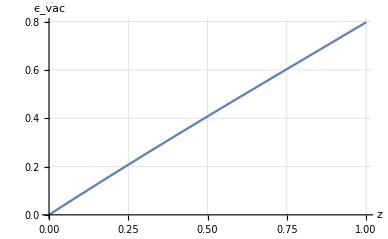

```mathematica
pl5=Plot[{hs33gen/.{α->4/3,γ->0.5}},{z,0,1},GridLines->Automatic,AxesLabel-> {"z","ϵ_vac"}]
```

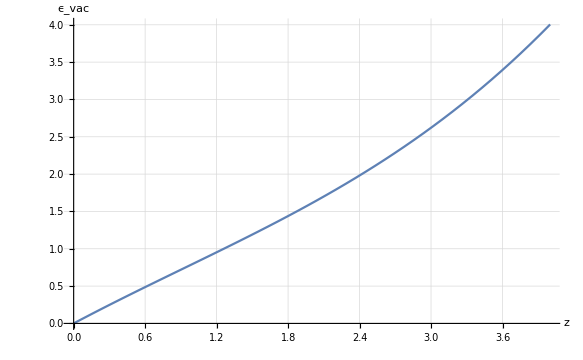

```mathematica
pl6=Plot[{hs33gen/.{α->4/3,γ->0.5}},{z,0,4},GridLines->Automatic,AxesLabel-> {Style["z",26],Style["ϵ_vac",26]},TicksStyle->Directive[FontSize->20]]
```

```mathematica
Export["hard_sphere_3-3",pl7,ImageSize->2000]
```

$Failed

```mathematica
Export["hard_sphere_comp_1.png",pl1]
Export["hard_sphere_comp_2.png",pl2]
Export["hard_sphere_2D.png",pl3]
```

hard_sphere_comp_1.png

```mathematica
"hard_sphere_comp_2.png"
```

hard_sphere_comp_2.png

```mathematica
pl7=Plot3D[{hs33gen/.{α->4/3}},{z,0,10},{γ,0,1},AxesLabel->{Style["z",26],Style["γ",26],Style["ϵ_vac",26]},TicksStyle->Directive[FontSize->15]]
```

-Graphics3D-

```mathematica
Export["hard_sphere_2D.png",pl7,ImageSize->2000]
```

hard_sphere_2D.png

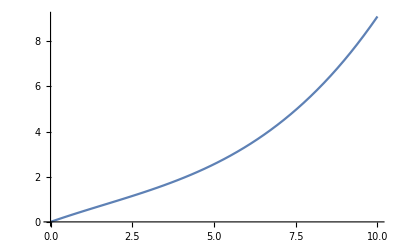

```mathematica
Plot[Evaluate[HS[4,2,0.5,z,4/3]],{z,0,10}]
```

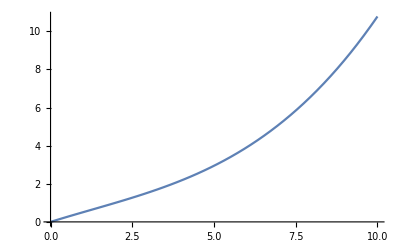

```mathematica
Plot[Evaluate[HS[4,3,0.5,z,4/3]],{z,0,10}]
```

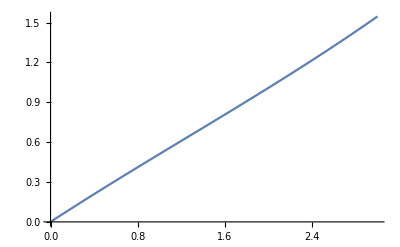

```mathematica
Plot[Evaluate[HS[4,3,0.5,z,4/3]],{z,0,3}]
```

```mathematica
Plot[Evaluate[HS[6,4,0.5,z,4/3]],{z,0,3}]
```

$Aborted

```mathematica
HS[4,2,0.01,z,4/3]
```

0.504035 z-0.0000155908 z^2+6.50353×10^-8 z^3+8.97394×10^-20 z^4